## Replicate Planck Plot

### Plotting Module

```mathematica
plotPotential[va_,left_,aList_,mark_,col_,lab_]:=Module[{p1,p2,ns60List,ns50List,r60List,r50List,ni,nf,ni2,nf2,n1guess,ϕsol2,ns,r,ϵ2,v,nsmin,nsmax,rmin,rmax},
ns60List={};ns50List={};r60List={};r50List={};
Do[
v[x_]:=va[x,a];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=CheckAbort[findϕsolnfLoop[v,v',v'',ni,nf,ni2,nf2,n1guess,False,False, left,0.2],Print["ABORTED"];Continue[]];
{ns,r,ϵ2} = findNsR[v,v',ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{a,aList}];
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[Legended[Transpose[{ns60List,r60List}],lab],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,20},PlotStyle->col];
p2 = ListPlot[Transpose[{ns50List,r50List}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{mark,12},PlotStyle->col];
Return[{p1,p2}]];
```

nff = -1.8

nff = -1.8

nff = -1.8

nff = -1.6

nff = -1.6

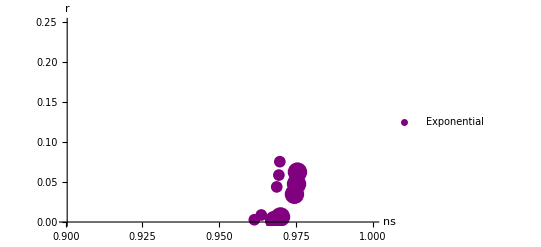

```mathematica
v[x_,a_]:=(0.01)*(1-Exp[-a*x]);
aList = {0.01,0.05,0.1,0.5,1};
{p14, p15} = plotPotential[v,False,aList,●,Purple,"Exponential"];
Show[p14,p15]
```

#### Hilltop Models: V=λ(ϕ^2 - σ^2)^2

nff = -1.8

nff = -1.8

nff = -1.8

«14 more identical outputs»

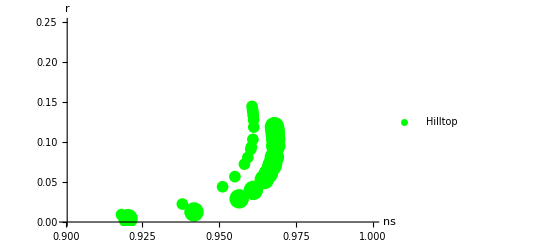

```mathematica
v[x_,a_]:=(0.01)*((x^2-(a)^2)^2 );
aList = {5,7,10,12,15,17,20,22,25,26,30,40,50,60,70,80,100};
{p1, p2} = plotPotential[v,True,aList,●,Green,"Hilltop"];
Show[p1,p2]
```

```mathematica
σList = {5,7,10,12,15,17,20,22,25,26,30,40,50,60,70,80,100};
ns60List={};ns50List={};r60List={};r50List={};
Do[
Print["σ = ",σ];
v[x_]:=(0.01)*((x^2-(σ)^2)^2 );
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60List,ns/.{n->60}];
AppendTo[ns50List,ns/.{n->50}];
AppendTo[r60List,r/.{n->60}];
AppendTo[r50List,r/.{n->50}];
,{σ,σList}]
```

σ = 5

ϕ0list = {-6.61037,-5.,-5.,-3.78194,3.78194,5.,5.,6.61037}

vacuumArray = {5.,5.}

InterpolatingFunction::dmval: Input value {-20.2786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.92786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.72026} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

σ = 7

ϕ0list = {-8.55564,-7.,-7.,-5.72721,5.72721,7.,7.,8.55564}

vacuumArray = {7.,7.}

σ = 10

ϕ0list = {-11.5137,-10.,-10.,-8.68529,8.68529,10.,10.,11.5137}

vacuumArray = {10.,10.}

σ = 12

ϕ0list = {-13.4973,-12.,-12.,-10.6688,10.6688,12.,12.,13.4973}

vacuumArray = {12.,12.}

σ = 15

ϕ0list = {-16.4807,-15.,-13.6523,13.6523,15.,16.4807}

vacuumArray = {15.}

σ = 17

ϕ0list = {-18.4729,-17.,-17.,-15.6445,15.6445,17.,17.,18.4729}

vacuumArray = {17.,17.}

σ = 20

ϕ0list = {-21.4642,-20.,-20.,-18.6357,18.6357,20.,20.,21.4642}

vacuumArray = {20.,20.}

σ = 22

ϕ0list = {-23.4596,-22.,-22.,-20.6312,20.6312,22.,22.,23.4596}

vacuumArray = {22.,22.}

σ = 25

ϕ0list = {-26.4542,-25.,-25.,-23.6258,23.6258,25.,25.,26.4542}

vacuumArray = {25.,25.}

σ = 26

ϕ0list = {-27.4526,-26.,-26.,-24.6242,24.6242,26.,26.,27.4526}

vacuumArray = {26.,26.}

σ = 30

ϕ0list = {-31.4475,-30.,-30.,-28.6191,28.6191,30.,30.,31.4475}

vacuumArray = {30.,30.}

σ = 40

ϕ0list = {-41.4392,-40.,-40.,-38.6108,38.6108,40.,40.,41.4392}

vacuumArray = {40.,40.}

σ = 50

ϕ0list = {-51.4342,-50.,-50.,-48.6058,48.6058,50.,50.,51.4342}

vacuumArray = {50.,50.}

σ = 60

ϕ0list = {-61.4309,-60.,-60.,-58.6025,58.6025,60.,60.,61.4309}

vacuumArray = {60.,60.}

σ = 70

ϕ0list = {-71.4285,-70.,-70.,-68.6001,68.6001,70.,70.,71.4285}

vacuumArray = {70.,70.}

σ = 80

ϕ0list = {-81.4267,-80.,-80.,-78.5983,78.5983,80.,80.,81.4267}

vacuumArray = {80.,80.}

σ = 100

ϕ0list = {-101.424,-100.,-100.,-98.5958,98.5958,100.,100.,101.424}

vacuumArray = {100.,100.}

{0.695701,0.841048,0.92033,0.941809,0.956532,0.96113,0.964736,0.966033,0.967164,0.967408,0.968017,0.968443,0.968441,0.968357,0.968263,0.968176,0.968034}

{2.18433×10^-8,0.0000681516,0.00417541,0.0125927,0.0290602,0.0396391,0.0531957,0.0606572,0.0698636,0.0724894,0.0812703,0.095403,0.103662,0.109035,0.112797,0.115575,0.119397}

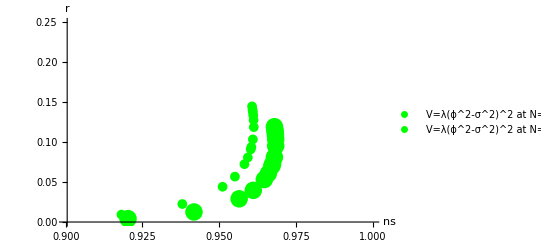

```mathematica
ns60List
r60List
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p1 = ListPlot[Legended[Transpose[{ns60List,r60List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Green];
p2 = ListPlot[Legended[Transpose[{ns50List,r50List}],"V=λ(ϕ^2-σ^2)^2 at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Green,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

Show[p1,p2]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

μ = 5

ϕ0list = {-5.75686,-4.34265,4.34265,5.75686}

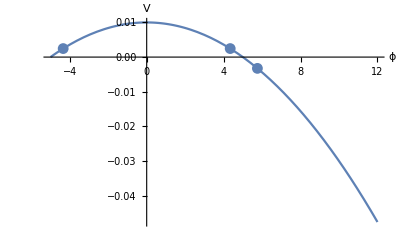

vacuumArray = {5.75686}

ϕ0 = 4.34265

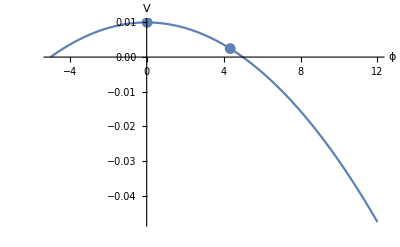

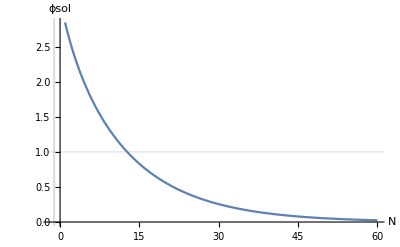

At n = 0, ϵ1 = 0.0765801

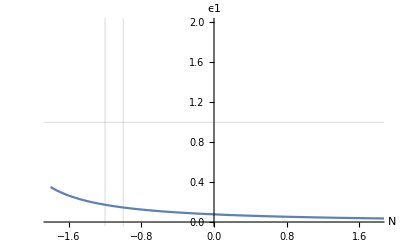

InterpolatingFunction::dmval: Input value {-8.25951} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.24628} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87798} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

At n1 = -2.2658, ϵ1 = 1.

ϕi2 = 0.0292652

ϕpi2 = -0.00228202

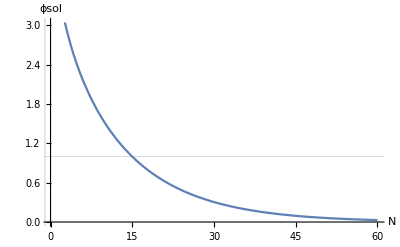

ϕsol2[60] = 0.0292652

μ = 7

ϕ0list = {-7.74273,-6.32852,6.32852,7.74273}

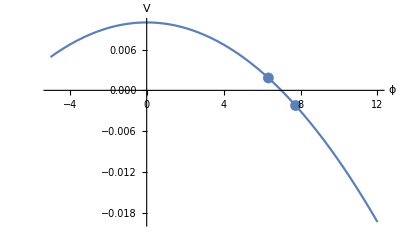

vacuumArray = {7.74273}

ϕ0 = 6.32852

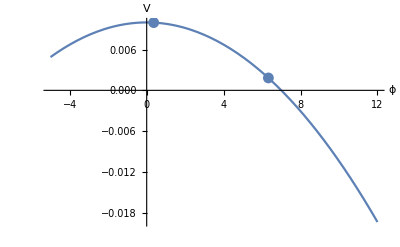

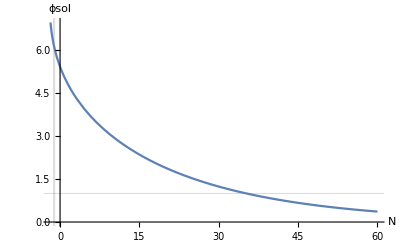

At n = 0, ϵ1 = 0.122593

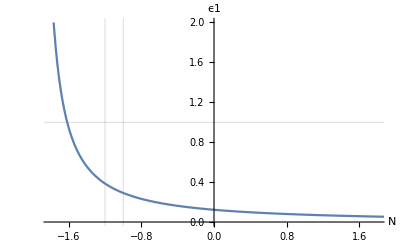

At n1 = -1.61669, ϵ1 = 1.

ϕi2 = 0.388381

ϕpi2 = -0.0156902

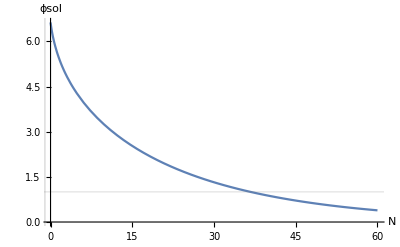

ϕsol2[60] = 0.388381

μ = 10

ϕ0list = {-10.7321,-9.31786,9.31786,10.7321}

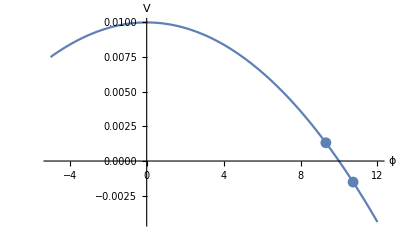

vacuumArray = {10.7321}

ϕ0 = 9.31786

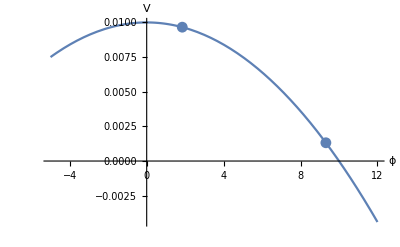

NDSolve::ndsz: At n == -1.65008, step size is effectively zero; singularity or stiff system suspected.

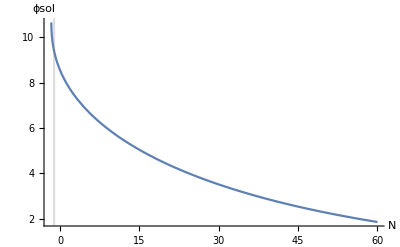

At n = 0, ϵ1 = 0.158567

Power::infy: Infinite expression 1/0. encountered.

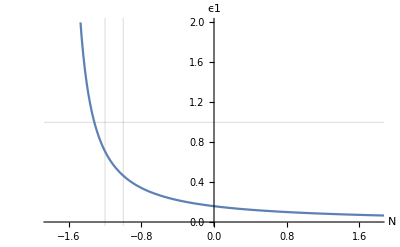

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-1.65241}.

At n1 = -1., ϵ1 = 0.464855

$Aborted

```mathematica
μList = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ={};ns50Listμ={};r60Listμ={};r50Listμ={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^2);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ,ns/.{n->60}];
AppendTo[ns50Listμ,ns/.{n->50}];
AppendTo[r60Listμ,r/.{n->60}];
AppendTo[r50Listμ,r/.{n->50}];
,{μ,μList}]
```

{0.844157,0.919048}

{0.000041661,0.00196946}

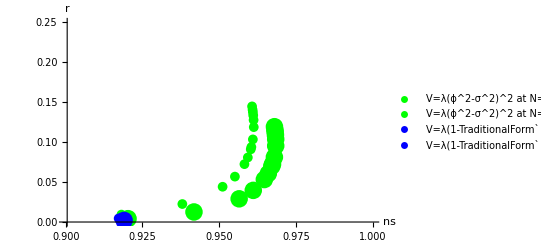

```mathematica
ns60Listμ
r60Listμ
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p3 = ListPlot[Legended[Transpose[{ns60Listμ,r60Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Blue];
p4 = ListPlot[Legended[Transpose[{ns50Listμ,r50Listμ}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Blue,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p1,p2,p3,p4]
```

### Hilltop Models: V=λ(1 - (ϕ/μ)^2 )

```mathematica
μ4List = {5,7,10,12,15,17,20,22,25,30,40,50,60,70,80,100};
ns60Listμ4={};ns50Listμ4={};r60Listμ4={};r50Listμ4={};
Do[
Print["μ = ",μ];
v[x_]:=(0.01)*(1-(x/μ)^4);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listμ4,ns/.{n->60}];
AppendTo[ns50Listμ4,ns/.{n->50}];
AppendTo[r60Listμ4,r/.{n->60}];
AppendTo[r50Listμ4,r/.{n->50}];
,{μ,μ4List}]
```

μ = 5

ϕ0list = {-5.88887,-4.41822,4.41822,5.88887}

vacuumArray = {5.88887}

InterpolatingFunction::dmval: Input value {-4.22929} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.46402} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.10549} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

μ = 7

ϕ0list = {-7.83,-6.38694,6.38694,7.83}

vacuumArray = {7.83}

μ = 10

ϕ0list = {-10.7896,-9.36129,9.36129,10.7896}

vacuumArray = {10.7896}

NDSolve::ndsz: At n == -1.75189, step size is effectively zero; singularity or stiff system suspected.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-2.16867}.

$Aborted

{0.954032,0.957231}

{0.000574391,0.00172612}

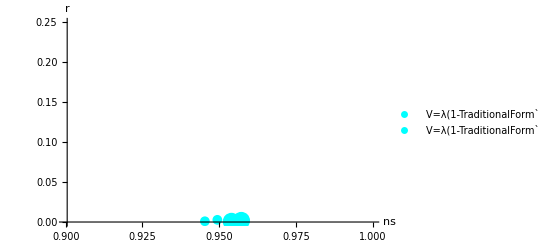

```mathematica
ns60Listμ4
r60Listμ4
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.25;
p5 = ListPlot[Legended[Transpose[{ns60Listμ4,r60Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,18},PlotStyle->Cyan];
p6 = ListPlot[Legended[Transpose[{ns50Listμ4,r50Listμ4}],"V=λ(1-TraditionalForm` ) at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,10},PlotStyle->Cyan,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];
Show[p5,p6]
```

### Natural Inflation Models: V=λ(1 + Cos(ϕ/ff) )

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-17.1129,-15.708,-14.3031,14.3031,15.708,17.1129}

vacuumArray = {15.708}

At n = 0, ϵ1 = 1.

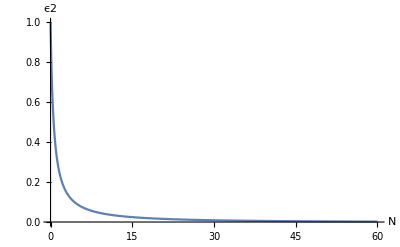

ns[60] = 0.953059

r[60] = 0.0325772

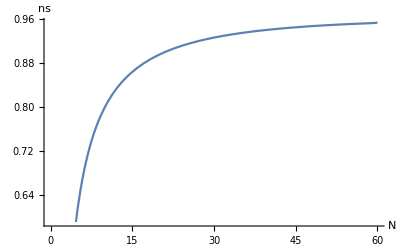

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve :: ratnz will be suppressed during this calculation.

ϕ0list = {-23.4006,-21.9911,-20.5817,20.5817,21.9911,23.4006}

vacuumArray = {21.9911}

At n = 0, ϵ1 = 1.

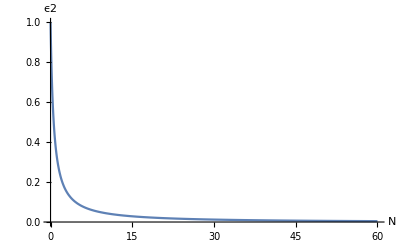

ns[60] = 0.963433

r[60] = 0.0686268

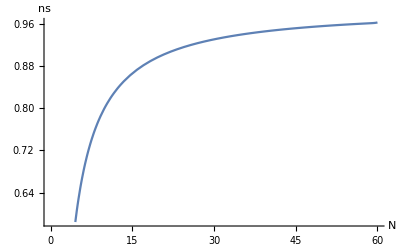

ϕ0list = {-32.8278,-31.4159,-30.0041,30.0041,31.4159,32.8278}

vacuumArray = {31.4159}

At n = 0, ϵ1 = 1.

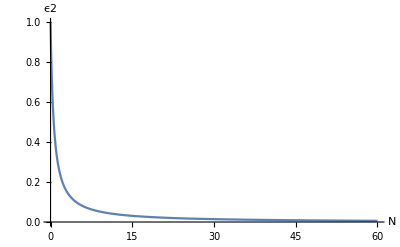

ns[60] = 0.966395

r[60] = 0.0979182

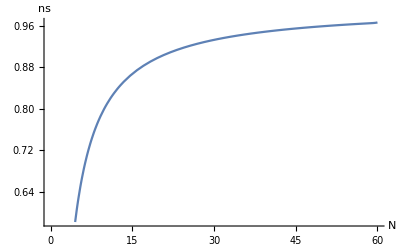

ϕ0list = {-39.1117,-37.6991,-36.2865,36.2865,37.6991,39.1117}

vacuumArray = {37.6991}

At n = 0, ϵ1 = 0.999975

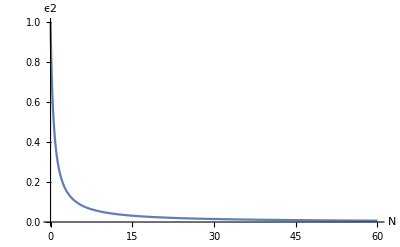

ns[60] = 0.966876

r[60] = 0.108062

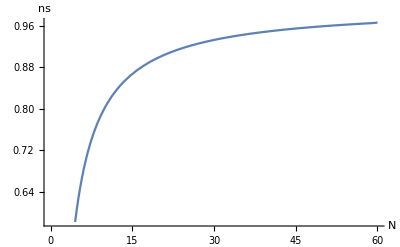

ϕ0list = {-48.5371,-47.1239,-45.7107,45.7107,47.1239,48.5371}

vacuumArray = {47.1239}

At n = 0, ϵ1 = 1.

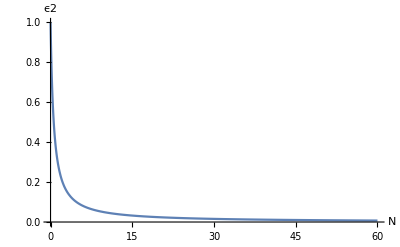

ns[60] = 0.967134

r[60] = 0.116905

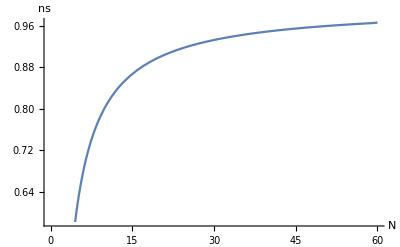

ϕ0list = {-54.8205,-53.4071,-51.9937,51.9937,53.4071,54.8205}

vacuumArray = {53.4071}

At n = 0, ϵ1 = 1.

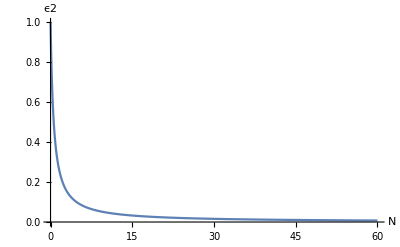

ns[60] = 0.967201

r[60] = 0.120522

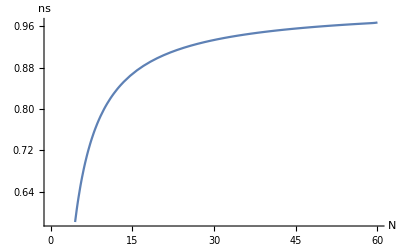

ϕ0list = {-64.2455,-62.8319,-61.4182,61.4182,62.8319,64.2455}

vacuumArray = {62.8319}

At n = 0, ϵ1 = 0.999998

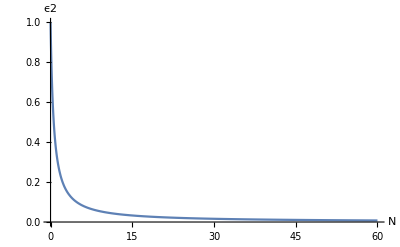

ns[60] = 0.967248

r[60] = 0.124124

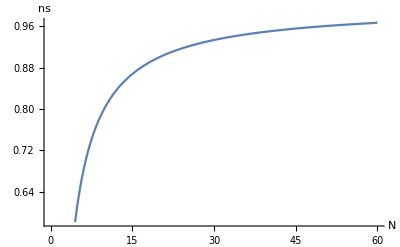

ϕ0list = {-70.5288,-69.115,-67.7013,67.7013,69.115,70.5288}

vacuumArray = {69.115}

At n = 0, ϵ1 = 1.

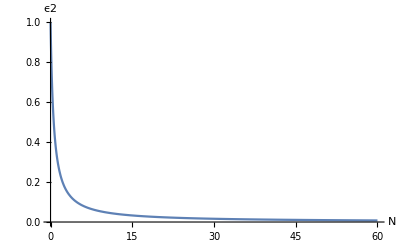

ns[60] = 0.967263

r[60] = 0.125776

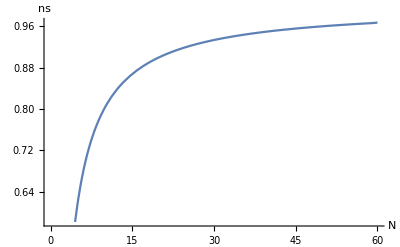

ϕ0list = {-79.9537,-78.5398,-77.126,77.126,78.5398,79.9537}

vacuumArray = {78.5398}

At n = 0, ϵ1 = 1.

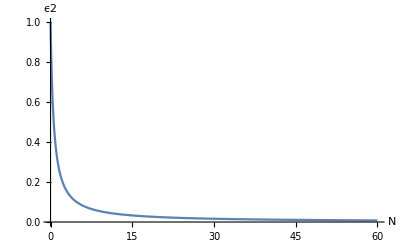

ns[60] = 0.967276

r[60] = 0.127567

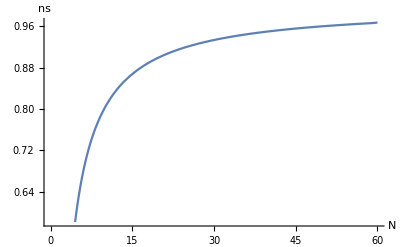

```mathematica
fList = {5,7,10,12,15,17,20,22,25};
ns60Listf={};ns50Listf={};r60Listf={};r50Listf={};
Do[
v[x_]:= 0.5*(0.01)*(1+Cos[x/ff]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, True];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,True,True]; 
AppendTo[ns60Listf,ns/.{n->60}];
AppendTo[ns50Listf,ns/.{n->50}];
AppendTo[r60Listf,r/.{n->60}];
AppendTo[r50Listf,r/.{n->50}];
,{ff,fList}]
```

{0.94761,0.956551,0.959096,0.95952,0.959754,0.959818,0.959865,0.959881,0.959895}

{0.0509702,0.0928376,0.124044,0.134515,0.143538,0.147203,0.150841,0.152505,0.154307}

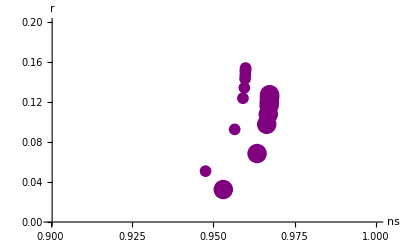

```mathematica
ns50Listf
r50Listf
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p5 = ListPlot[Transpose[{ns60Listf,r60Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=60"}]];
p6 = ListPlot[Transpose[{ns50Listf,r50Listf}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple,PlotLegends->PointLegend[Automatic,{"Hilltop at N=50"}]];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p5,p6]
```

### Starobinsky’s R^2 Model: V(ϕ)=M_pl^2/(4α)(1-exp[-√(2/3)ϕ/M_pl])^2

```mathematica
v[x_]:=(0.1)*(1-Exp[-√(2/3)*x])^2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.,0.940178}

vacuumArray = {0.}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

ϕi1s = {5.45315}

InterpolatingFunction::dmval: Input value {-2.34373} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.95601} lies outside the range of data in the interpolating function. Extrapolation will be used.

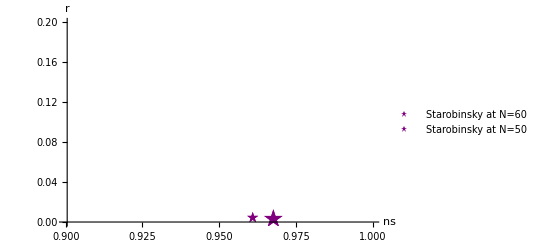

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p7 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Starobinsky at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Purple];
p8 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Starobinsky at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p7,p8]
```

### Shaposhnikov model: V(ϕ)=λM_pl^2/(4 ξ^2)(1+exp[(-2ϕ)/(√6 M_pl)])^-2

```mathematica
v[x_]:=(0.1)*(1+Exp[-2*x/√6])^-2;
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-2.2857}

vacuumArray = {}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕi1s = {5.27113}

InterpolatingFunction::dmval: Input value {-1.81269} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87451} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.87534} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

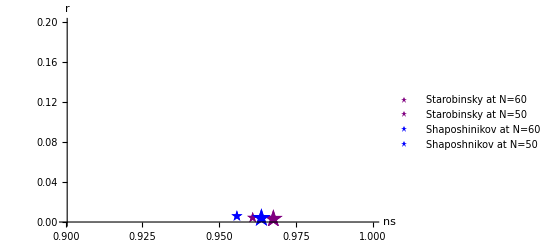

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p9 = ListPlot[Legended[Thread[{{ns/.{n->60}},{r/.{n->60}}}],"Shaposhinikov at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,20},PlotStyle->Blue];
p10 = ListPlot[Legended[Thread[{{ns/.{n->50}},{r/.{n->50}}}],"Shaposhnikov at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{★,12},PlotStyle->Blue];
Show[p7,p8,p9,p10]
```

### D-brane inflation: V(ϕ)=λ^4(1-(m/ϕ)^p)

```mathematica
mList = {1,10,20,40,60,80,100};
pList={1,2,3,4};
colorList = {Red,Green,Blue,Orange}; jj=1;
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2; p11={};p12={};
Do[ns60Listm={};ns50Listm={};r60Listm={};r50Listm={};
Do[
Print["m = ",m];
Print["jj = ",jj];
v[x_]:=(0.01)*(1-(m/x)^p);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listm,ns/.{n->60}];
AppendTo[ns50Listm,ns/.{n->50}];
AppendTo[r60Listm,r/.{n->60}];
AppendTo[r50Listm,r/.{n->50}];
,{m,mList}]
AppendTo[p11, ListPlot[Legended[Transpose[{ns60Listm,r60Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,20},PlotStyle->colorList[[jj]]]];
AppendTo[p11 , ListPlot[Legended[Transpose[{ns50Listm,r50Listm}],StringJoin["D-brane p=",ToString[p]," at N=60"]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{▲,12},PlotStyle->colorList[[jj]]]];
jj = jj+1;
,{p,pList}];

Show[p11]
```

m = 1

jj = 1

ϕ0list = {-0.478318,1.47832}

vacuumArray = {}

ϕi1s = {6.19259}

NDSolve::ndsz: At n == -1.48307, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-1.65263} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-1.65263}.

$Aborted

Show::shx: No graphical objects to show.

Show[{}]

### Exponential potential: V(ϕ)=λ^4(1-exp[-qϕ/M_pl])

```mathematica
qList = {0.01,0.05,0.1,0.5,1};
ns60Listq={};ns50Listq={};r60Listq={};r50Listq={};
Do[
v[x_]:=(0.01)*(1-Exp[-q*x]);
vp[x_]=v'[x];
vpp[x_] = v''[x];

ni = 60; (* initial value f n for integration *)
nf = -1.8; (* final value of n for integration *)
ni2 = 60;
nf2 = 0;
n1guess = -1;

ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False, False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[ns60Listq,ns/.{n->60}];
AppendTo[ns50Listq,ns/.{n->50}];
AppendTo[r60Listq,r/.{n->60}];
AppendTo[r50Listq,r/.{n->50}];
,{q,qList}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-0.709619,0.704619}

vacuumArray = {}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

ϕi1s = {10.7799}

NDSolve::ndsz: At n == -1.40465, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-0.719909,0.694894}

vacuumArray = {}

ϕi1s = {10.058}

NDSolve::ndsz: At n == -1.43912, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-0.733352,0.683226}

vacuumArray = {}

ϕi1s = {9.28616}

NDSolve::ndsz: At n == -1.47769, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

ϕ0list = {-0.872529,0.605467}

vacuumArray = {}

ϕi1s = {5.88835}

InterpolatingFunction::dmval: Input value {-1.92224} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {n} = {-1.92224}.

$Aborted

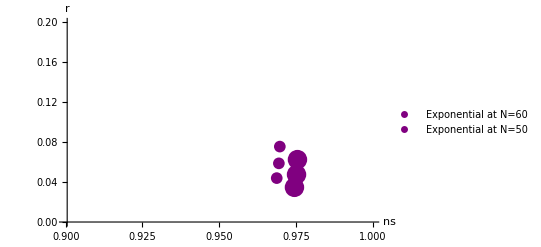

```mathematica
nsmin = 0.9; nsmax = 1; rmin = 0; rmax = 0.2;
p12 = ListPlot[Legended[Transpose[{ns60Listq,r60Listq}],"Exponential at N=60"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->Purple];
p13 = ListPlot[Legended[Transpose[{ns50Listq,r50Listq}],"Exponential at N=50"],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->Purple];

(* Show[p1,p2,p3,p4,p5,p6] *)
Show[p12,p13]
```

### Spontaneously Broken SUSY: V(ϕ)=λ^4(1+a*log[ϕ/M_pl])

## Monomial Loop for Planck Plot

ϕ0list = {-1.41421,0,1.41421}

vacuumArray = {0}

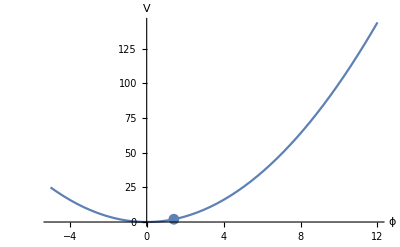

ϕ0list = {-0.471405,0.471405}

vacuumArray = {}

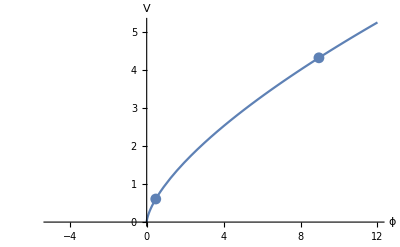

NDSolve::ndsz: At n == -1.61847, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-0.707107,0.707107}

vacuumArray = {}

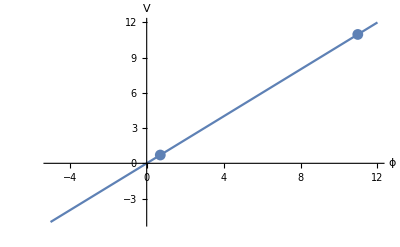

NDSolve::ndsz: At n == -1.39548, step size is effectively zero; singularity or stiff system suspected.

ϕ0list = {-2.12132,0,2.12132}

vacuumArray = {0}

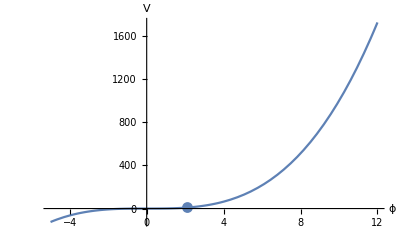

ϕ0list = {-2.82843,0,2.82843}

vacuumArray = {0}

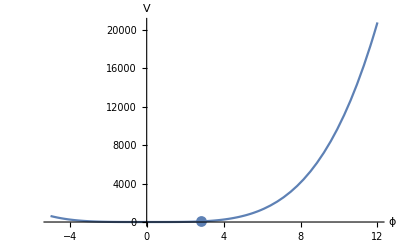

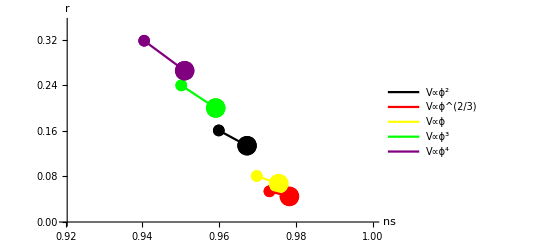

```mathematica
(* Loop over several monomial potentials and generate and ns vs r plot *)
ni = 60; nf = -1.8; ni2 = 60; nf2 = 0; n1guess = -1;
pList = {2,2/3,1,3,4};plotList = {}; 
clrList = {Black,Red,Yellow,Green,Purple}; ii=1;
nsmin = 0.92; nsmax = 1; rmin = 0; rmax = 0.35;
Do[
Clear[v,vp,vpp,ns,r,ϵ2];
v[x_] := x^p;
vp[x_]=v'[x];
vpp[x_] = v''[x];
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,False];
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,False]; 
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->50}},{r/.{n->50}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,12},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,{"N=50"},LegendFunction->"Frame"]]];
AppendTo[plotList,ListPlot[Thread[{{ns/.{n->60}},{r/.{n->60}}}],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotMarkers->{●,20},PlotStyle->clrList[[ii]],PlotLegends->PointLegend[Automatic,"N=60",LegendFunction->"Frame"]]];
AppendTo[plotList,ListLinePlot[Legended[{{ns/.{n->50},r/.{n->50}},{ns/.{n->60},r/.{n->60}}},V∝ϕ^pList[[ii]]],PlotRange->{{nsmin,nsmax},{rmin,rmax}},
AxesLabel->{"ns","r"},PlotStyle->clrList[[ii]]]];
ii = ii+1,{p,pList}]
Show[plotList]
```